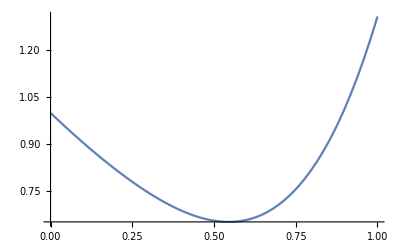

Minimize::ivar: 0.544919 is not a valid variable.

NMinimize::ivar: 0.544919 is not a valid variable.

NMinimize[0.6532,0.544919]

```mathematica
(* Demo by Jose Bento @ BC *)
(*References, on my webpage,    Testing fine-grained parallelism for the ADMM on a factor-graph . See also references cited therein*)
(*Imagine we want to solve the following problem*)
f[x_]:=-Log[1+x];
g[x_]:=1+x^4;
Plot[f[x]+g[x],{x,0,1}]
Minimize[f[x]+g[x],x]//N
```

```mathematica
(*Imagine that solving Min[f[x],x] it self is easy and that solving Min[g[x],x] is easy, specially when f and g are nice smooth functions, but that solving Min[f[x],x] and Min[g[x],x], when f and g are not smooth is not that easy, and that, specially, Min[f[x] + g[x],x] is not that easy to solve. What can we do?*)
(*Let us perform a series of --apparent-- complications*)
Remove[x,y,z];
FindMinimum[f[x]+g[x],{x,0.1}]//N
FindMinimum[{f[x]+g[y],x==z&&y==z},{{x,0.1},{y,0.1},{z,0.1}}]//N
FindMinimum[{f[x]+g[y]+1/2(x-z)^2+1/2(y-z)^2,x==z&&y==z},{{x,0.1},{y,0.1},{z,0.1}}]//N
```

{0.6532,{x→0.544933}}

{0.6532,{x→0.544933,y→0.544933,z→0.544933}}

{0.6532,{x→0.544933,y→0.544933,z→0.544933}}

```mathematica
(*Let us now make use of duality to solve the last of the problems above. Duality tells us that to solve Min[{f[x],h[x]==0},x] we can solve Max[L[λ],λ] where L[λ] = Min[f[x]+λh[x],x]. Notice in particular that we are now solving only unconstrained problems.
Using duality, the new unconstrained problem is a MaxMin problem namely, Max[  Min[f[x]+λh[x],x]  , λ] *)
Remove[x,y,z,λ1,λ2]
L[λ1_,λ2_]:=FindMinimum[{f[x]+g[y]+1/2(x-z)^2+1/2(y-z)^2+λ1*(x-z)+λ2*(y-z)},{{x,0.5},{y,0.5},{z,0.5}}];
(*Plot L to find the maximum because the function is numerically strange and hard to optimize using Mathematica's solvers*)
Plot3D[L[λ1,λ2][[1]],{λ1,0.4,0.8},{λ2,-0.8,-0.4}]
(*It turns out that the max is at λ1=-λ2=646151. For this value, we now extract the solution. It matches the intial one*)
L[0.6472770986241363,-0.6472770986241363]
```

-Graphics3D-

{0.6532,{x→0.544933,y→0.544933,z→0.544933}}

```mathematica
(*The point is...we have made a series of manipulation that lead to problems that all have the same solution. A bit strange...but will make sense soon.*)
```

```mathematica
(*To solve this MaxMin problem, we are going to proceed in rounds. In each round, we optimize the objective over x, y and z, one at a time, and we perform gradient ascent steps on λ1 and λ2  *)
(*Recall that the equivalent problem we are trying to solve is Max[  Min[ FL[x,y,z,λ1,λ2] ,{x,y,z}]  ,{λ1,λ2} ], where FL is give by*)
FL[x_,y_,z_,λ1_,λ2_]:=f[x]+g[y]+1/2(x-z)^2+1/2(y-z)^2+λ1*(x-z)+λ2*(y-z);
(*Start with some initial values*)
x = 1;
y=1;
z =1;
λ1 = 1;
λ2=1;
(*Optimization over x*)
x=Minimize[ FL[s,y,z,λ1,λ2],s][[2,1,2]]//N;
(*Notice that this is actually the same as *)
x=Minimize[ f[s]+1/2(s-(z-λ1))^2,s][[2,1,2]]//N;
(*Optimization over y*)
y=Minimize[FL[x,s,z,λ1,λ2],s][[2,1,2]]//N;
(*Notice that this is actually the same as *)
y=Minimize[g[s]+1/2(s-(z-λ2))^2,s][[2,1,2]]//N;
(*Optimization over z*)
z=Minimize[ FL[x,y,s,λ1,λ2],s][[2,1,2]]//N;
(*Notice that this is actually the same as *)
z=((x+λ1)+(y+λ2))/2;
(*Make a gradient step over λ1 and λ2*)
alpha=0.1;
λ1=λ1+alpha*(x-z);
λ2=λ2+alpha*(y-z);
(*Repeat until the variables converge to some value*)
```

```mathematica
(*A few important observations.
First, appart from the first two updates, all the other updates are very very simple. They are just some linear equations. 
Second, in each iteration we need to solve two optimization problems. However, each of these optimization problems only involves ONE function. Either f or g. Furthermore, the objectives in these problems of "smooth" because they are of the form "something + quadratic". Hence, they are well behaved for numerical optimization, even when f and g are not.
Third, we have traded solving ONE complex problem for solving a sequence of simpler problems.
*)
```

```mathematica
(*The simple problems have closed form solution *)
Remove[s,n];
(*Let us solve the first problem. Just take the derivative and make it equal to zero.*)
Solve[D[ f[s]+1/2(s-n)^2,s]==0,s]//FullSimplify
(*Let us solve the second problem. Just take the derivative and make it equal to zero.*)
Solve[D[ g[s]+1/2(s-n)^2,s]==0,s]//FullSimplify
```

{{s→1/2 (-1+n-√(5+n (2+n)))},{s→1/2 (-1+n+√(5+n (2+n)))}}

{{s→(-3^(2/3)+3^(1/3) (9 n+√(3+81 n^2))^(2/3))/(6 (9 n+√(3+81 n^2))^(1/3))},{s→(3 ⅈ+√3-3^(1/6) (9 n+√(3+81 n^2))^(2/3)+ⅈ 3^(2/3) (9 n+√(3+81 n^2))^(2/3))/(4 3^(5/6) (9 n+√(3+81 n^2))^(1/3))},{s→(3^(1/3)-ⅈ 3^(5/6)-(1+ⅈ √3) (9 n+√(3+81 n^2))^(2/3))/(4 3^(2/3) (9 n+√(3+81 n^2))^(1/3))}}

```mathematica
(*So now we can write our iterations as follows*)
```

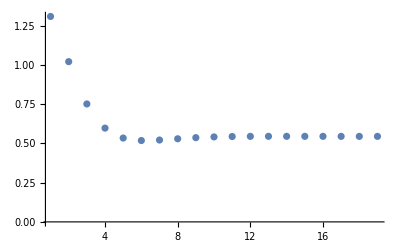

0.544932

```mathematica
(*Start with some initial values*)
x = 1.0;
y=1.0;
z =1.0;
λ1 = 1.0;
λ2=1.0;
evolz={};
alpha=1.0;
For[i=1,i<20,i++,{
(*Optimization over x*)
n=z-λ1;
x=1/2 (-1+n+√(5+n (2+n)));
(*Optimization over y*)
n=z-λ2;
y=(-3^(2/3)+3^(1/3) (9 n+√(3+81 n^2))^(2/3))/(6 (9 n+√(3+81 n^2))^(1/3));
(*Optimization over z*)
z=((x+λ1)+(y+λ2))/2;
(*Make a gradient step over λ1 and λ2*)
λ1=λ1+alpha*(x-z);
λ2=λ2+alpha*(y-z);
AppendTo[evolz,z];
}];
ListPlot[evolz,PlotRange->All]
Print[z];
```

(*We have just solved our first problem using the Alternating Direction Method of Multipliers, aka ADMM*)
(*Let us summarize what we saw*)
(*To solve...*)

Minimize[f_1[x]+f_2[x],x]
(*We do, repeatidely, after a few renamings and introducing an extra parameter ρ.....*)
x_1=Minimize[f_1[s]+ρ/2(s-(z-λ_1))^2,s][[2,1,2]]//N;
x_2=Minimize[f_2[s]+ρ/2(s-(z-λ_2))^2,s][[2,1,2]]//N;
z=((λ_1+x_1)+(λ_2+x_2))/2
λ_1=λ_1+α*( x_1-z)
λ_2=λ_2+α*( x_2-z)

```mathematica
(*This can be easily generalized to deal with the sum of many functions*)
(*If we want to solve ...*)
```

Minimize[∑_(i=1)^n f_i[x],x]
(*We do, repeatidely....*)
x_1=Minimize[f_1[s]+ρ/2(s-(z-λ_1))^2,s][[2,1,2]]//N;
x_2=Minimize[f_2[s]+ρ/2(s-(z-λ_2))^2,s][[2,1,2]]//N;
x_3=Minimize[f_3[s]+ρ/2(s-(z-λ_3))^2,s][[2,1,2]]//N;
(*...*)
x_n=Minimize[f_n[s]+ρ/2(s-(z-λ_n))^2,s][[2,1,2]]//N;
z=((λ_1+x_1)+(λ_2+x_2)+...+(λ_n+x_n))/n
λ_1=λ_1+α*(x_1-z)
λ_2=λ_2+α*(x_2-z)
λ_3=λ_3+α*(x_3-z)
(*...*)
λ_n=λ_n+α*(x_n-z)

```mathematica
(*Notice that we have reduced solving ONE complex problem, possibly non smooth, to solving a series of simpler problems, each only involving one of the functions Subscript[f, i]. There problems are smooth. Furthermore, notice that these problems can all be solved in PARALLEL. The summation inside the Z-update step can also be parallelize. And the different λ-updates can also be parallized.*)
```

```mathematica
(*Let us see this in action by solving a simple SVM problem*)
(*Switch to Matlab for convinience*)
```